```mathematica
f[t_]:=t
a=1;
g1[t_]:=0.5 Cos[t/π]
g2[t_]:=0.5Sin[t/π]
```

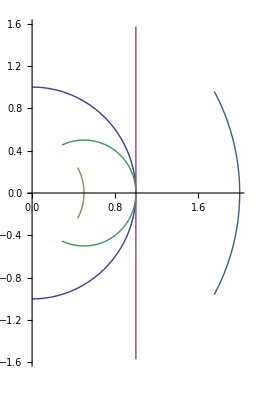

```mathematica
ParametricPlot[
{
{Cos[t],Sin[t]},
{a,f[t]},
{g1[t],g2[t]},
{1/Norm[{f[t],a}] Cos[ArcTan[f[t]/a]],1/Norm[{f[t],a}] Sin[ArcTan[f[t]/a]]},
{1/Norm[{g1[t],g2[t]}] Cos[ArcTan[g2[t]/g1[t]]],1/Norm[{g1[t],g2[t]}] Sin[ArcTan[g2[t]/g1[t]]]}
},{t,-π/2, π/2}]
```

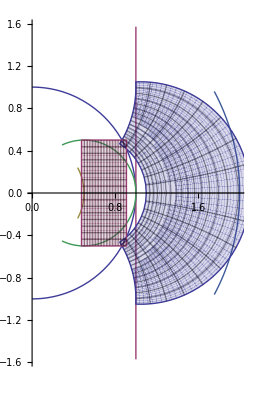

```mathematica
Show[
ParametricPlot[
{
{Cos[t],Sin[t]},
{a,f[t]},
{g1[t],g2[t]},
{1/Norm[{f[t],a}] Cos[ArcTan[f[t]/a]],1/Norm[{f[t],a}] Sin[ArcTan[f[t]/a]]},
{1/Norm[{g1[t],g2[t]}] Cos[ArcTan[g2[t]/g1[t]]],1/Norm[{g1[t],g2[t]}] Sin[ArcTan[g2[t]/g1[t]]]}
},{t,-π/2, π/2}],
ParametricPlot[{
{1/Norm[x+y ⅈ] Cos[-Arg[x+y ⅈ]],1/Norm[x+y ⅈ] Sin[-Arg[x+y ⅈ]]},
{Norm[x+y ⅈ]Cos[Arg[x+y ⅈ]],Norm[x+y ⅈ]Sin[Arg[x+y ⅈ]]}
}
,{x,1/2.1,1/1.1},{y,-0.5,0.5},AspectRatio->1]
]
```